# Thesis Notebook

## 2D Orbit with the improved Tolman VII neutron star density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

## Star constants

```mathematica
(*From wikipedia paper*)
```

```mathematica
Msol = 1.989 10^30;
G = 6.6743 10^-11;
c = 3 10^8;
```

```mathematica
Mdummy = (G 1.4Msol)/c^2
```

2065.03

```mathematica
Rdummy = (16 10^3)/Mdummy;
```

```mathematica
infprec[lowlyprecision_, p_] := 10^-p Round[(10^p) lowlyprecision]
R = infprec[Rdummy, 10];
```

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = R;(*Radius of the Star*)
M = 1;
R // N
```

7.74808

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r)

```mathematica
rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

```mathematica
rbarStar = rbarofrOutside[RStar];
```

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2;
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

```mathematica
A[rbarStar]//N
```

1.15456

## Tolman VII improved Isotropic coords definitions

### Constants

```mathematica
ScriptC = M/RStar;
```

### Universal alpha factor

```mathematica
a1 = infprec[3.70625, 60];
a2 = infprec[1.50266, 60];
a3 = infprec[0.0643875,60];
n = infprec[.903, 60];

Precision[{a1, a2, a3, n}]
```

∞

```mathematica
alphaaaFunc[a1_, a2_, a3_, n_] :=a1 -a2(ScriptC^n/(rho0*RStar^2))+a3(ScriptC^n/(rho0*RStar^2))^2 ;
```

```mathematica
alphaaa= alphaaaFunc[a1, a2, a3, n];
```

```mathematica
(*alphadummy = infprec[alphaadummy, 60];*)
```

```mathematica
(*alphaaa = SetPrecision[alphadummy, 60];*)
```

### New interior rho

```mathematica
Clear[rho0]
rhoInside[r_] := rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)
```

```mathematica
massIntegral =  4 Pi Integrate[rhoInside[r] r^2, {r, 0, RStar}];
```

```mathematica
N[%]
```

12.5664 (0.104731-0.0000117675/rho0-9.91187 rho0)

```mathematica
sol = Solve[massIntegral == 1, rho0];
rho0 = rho0 /. sol[[2]];(*Larger density seems more realistic for neutron star*)
```

```mathematica
rho0 //N
```

0.00191905

```mathematica
Precision[rho0]
```

∞

### New mass function

```mathematica
MassFuncInside[r_] := 4 Pi rho0 RStar^3 ( 1/3(r/RStar)^3 - alphaaa/5(r/RStar)^5 + ((alphaaa-1)/7)(r/RStar)^7)
```

## Numerically integrating for the pressure and the phi in α = exp(phi)

### Defining the ODEs

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -(rhoInside[r] + Pressure)((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := ((MassFuncInside[r] + 4 Pi Pressure r^3)/(r(r-2MassFuncInside[r])));
```

#### Numerically integrating these coupled ODEs

```mathematica
rmin = 10^-16;
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
BCs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
BCs},
{P, Phi},
{r, RStar, rmin},
WorkingPrecision->50
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

NDSolve::nderr: Error test failure at r == 7.6981960337012198169800956387795826214281702497903; unable to continue.

```mathematica
eq1[[2]]//Precision
```

∞

```mathematica
Pressure[r_] := P[r] /. sol1

PhiMetric[r_] = Phi[r] /. sol1;
```

InterpolatingFunction::dmval: Input value {0.000158282} lies outside the range of data in the interpolating function. Extrapolation will be used.

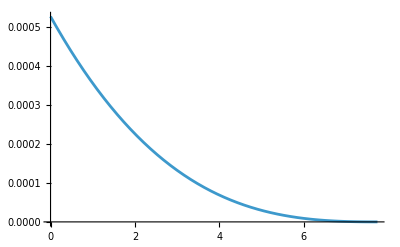

```mathematica
Plot[Pressure[r], {r, 0, RStar}, PlotRange->All]
```

## Solving for r̄(r) and r(r̄) inside

### Defining the ODE

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
```

### Numerically Integrating the above equation

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, RStar, rmin},
WorkingPrecision->50
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

```mathematica
Precision[rbarofrInside[4]]
```

49.2388

#### Some sanity checks

```mathematica
Precision[rbarofrInside[RStar]]
Precision[rbarofrOutside[RStar]]
```

49.6653

∞

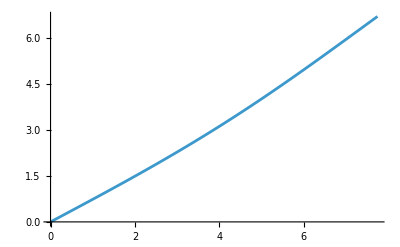

```mathematica
Plot[rbarofrInside[r], {r, 0, RStar}]
```

### Now using the interpolation trick to obtain r(r̄): (causing issues?)

```mathematica
(*Table[ expression, {variable, start, end, step}*)
data = Table[
{rbarofrInside[r], r}, 
{r, rmin, RStar, (RStar - rmin)/10000} (*10000 points and A is not messy*)
];
```

```mathematica
rofrbarInside = Interpolation[data];
```

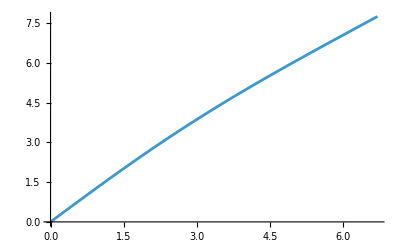

```mathematica
Plot[rofrbarInside[rbar], {rbar, 0, rbarStar}]
```

## Finding the interior metric functions

### Getting αInside(r̄):

```mathematica
αInside[rbar_] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

#### Sanity checks

InterpolatingFunction::dmval: Input value {0.0000139091} lies outside the range of data in the interpolating function. Extrapolation will be used.

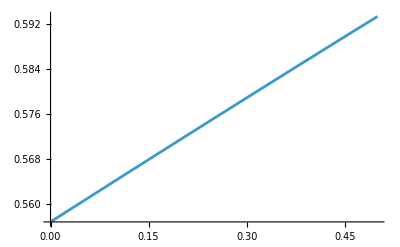

```mathematica
Plot[αInside[rbar], {rbar, 0, .5}]
```

```mathematica
αInside[rbarStar]
α[rbarStar] //N
```

0.86131959660716915269485968805729870536001682209556

0.86132

```mathematica
αFull[rbar_] := Piecewise[
{
{αInside[rbar], rbar < rbarStar},
{α[rbar], rbar >= rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {0.000186683} lies outside the range of data in the interpolating function. Extrapolation will be used.

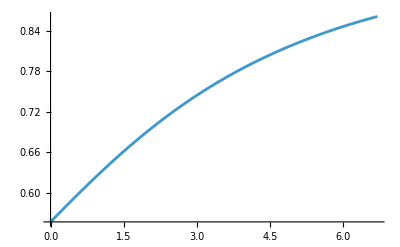

```mathematica
Plot[αFull[rbar], {rbar, 0, rbarStar}]
```

### Making the derivative of alpha continuous

#### Interior derivative in terms of r

Doing things in r first as this is more analytic

```mathematica
dPhidrMetric[r_] := ((MassFuncInside[r] + 4 Pi Pressure[r] r^3)/(r(r-2MassFuncInside[r])))
```

```mathematica
alpha[r_] := Exp[PhiMetric[r]]
DERalphaIns[r_] := dPhidrMetric[r] alpha[r] (*Something analytic times a numerical integral*)
```

#### Exterior derivative in terms of r

```mathematica
DERαOutsiderbardummy = Derivative[1][α][rbar];
DERαOutsiderbar[r_] := ((1-1/(2 rbar))/(2 (1+1/(2 rbar))^2 rbar^2)+1/(2 (1+1/(2 rbar)) rbar^2) )/. rbar -> rbarofrOutside[r] (*More accurate subbing in after for rbar maybe?*)
drbardr[r_] := rbarofrOutside[r]/r(1 - (2M)/r)^(-1/2)
```

```mathematica
DERalpha[r_] := drbardr[r]  DERαOutsiderbar[r] (*Chain rule*)
```

#### Sanity check at boundary

```mathematica
DERalpha[RStar] //N
DERalphaIns[RStar] //N
```

0.0193396

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating ((-455364912443911862283130176365375518798828125+«1»+√(3 (69119067828350505468561708388668045855737534738198746264714600329170934855937957763671875-«1»+78070304686534528318840998823423585201879383874986685414865722479047944982515129778176 2^(«1») 3^(«1») 5^(«1») 1076121859^(«1») π^2))) (1/3+1/7 («1»)+1/5 («1»)))/19407218887490519374432245296574716388927160.

0.0193396

```mathematica
DERalphaIns[rofrbarInside[rbarStar]]
DERalpha[rofrbarInside[rbarStar]]
```

0.019339612693838799929026533566452946302957025776

0.01933961269383879992902653356645294630295702577574

InterpolatingFunction::dmval: Input value {7.25074} lies outside the range of data in the interpolating function. Extrapolation will be used.

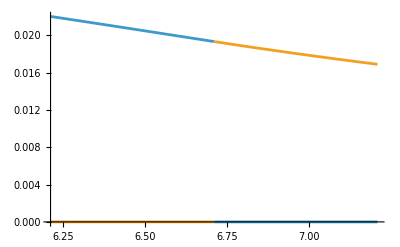

```mathematica
Plot[{Piecewise[{{DERalphaIns[rofrbarInside[rbar]],rbar<=rbarStar}}],Piecewise[{{DERalpha[rofrbarOutside[rbar]],rbar>=rbarStar}}]},{rbar,rbarStar-0.5,rbarStar+0.5}]
```

InterpolatingFunction::dmval: Input value {7.59893} lies outside the range of data in the interpolating function. Extrapolation will be used.

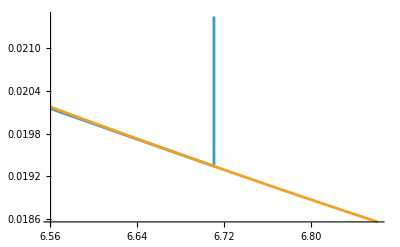

```mathematica
Plot[{DERalphaIns[rofrbarInside[rbar]],DERalpha[rofrbarOutside[rbar]]},{rbar,rbarStar-0.15,rbarStar+0.15}]
```

#### I messed up coordinate transforms here, that’s why the numbers were off.

```mathematica
(*DERalpha[rbarofrOutside[RStar]] //N (*Think I am making a mess of coordinate tranforms here as they are the same above and in the graph*)
DERalphaIns[rbarofrInside[RStar]] //N (*More or less continuous now but not exact*)*)
```

```mathematica
(*diff = Abs[1 - DERalphaIns[rbarofrInside[RStar]]/DERalpha[rbarofrOutside[RStar]]]*)
```

```mathematica
(*Abs[Log10[diff]] (*Amount of digits in agreement*)*)
```

### Isotropic coordinates DERα definitions

```mathematica
DERαOutside[rbar_] := Module[{r = rofrbarOutside[rbar]}, drbardr[r]  DERαOutsiderbar[r]]

DERαInside[rbar_] := Module[{r = rofrbarInside[rbar]},
dPhidrMetric[r] alpha[r]]
```

```mathematica
DERαFull[rbar_] := Piecewise[
{
{DERαInside[rbar], rbar < rbarStar},
{DERαOutside[rbar], rbar >= rbarStar}
}
]
```

#### Sanity checks

```mathematica
DERαInside[rbarStar]
```

0.019339612693838799929026533566452946302957025776

```mathematica
DERαOutside[rbarStar] //N
```

0.0193396

```mathematica
(*DERαFull[rbar_]:=If[rbar<rbarStar,DERαInside[rbar],DERαOutside[rbar]]*)
```

InterpolatingFunction::dmval: Input value {0.000556365} lies outside the range of data in the interpolating function. Extrapolation will be used.

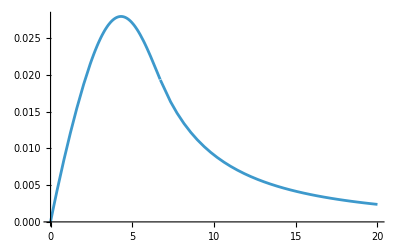

```mathematica
Plot[DERαFull[rbar], {rbar, 0, 20}]
```

### Getting AInside(r̄):

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

#### Sanity checks

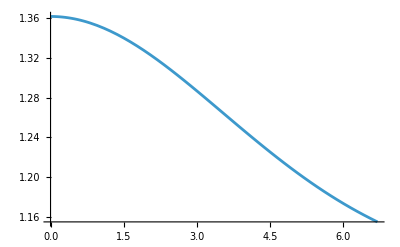

```mathematica
Plot[AInside[rbar], {rbar, 0, rbarStar}]
```

```mathematica
A[rbarStar] // N
AInside[rbarStar]
```

1.15456

1.154564212617279070545453059892637784277929747596

```mathematica
AFull[rbar_] := Piecewise[
{
{A[rbar], rbar >= rbarStar},
{AInside[rbar], rbar < rbarStar}
}
];
```

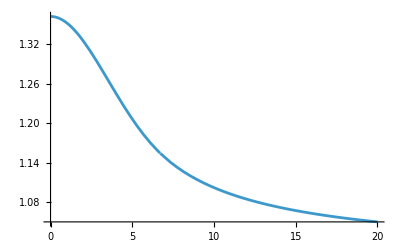

```mathematica
Plot[AFull[rbar], {rbar, 0, 20}]
```

### Isotropic coordinates definitions of DERA:

#### Inside

```mathematica
drbardr[rbar_, r_] := rbar/r(1 - (2MassFuncInside[r])/r)^(-1/2)
drdrbar[rbar_] := rofrbarInside[rbar]/rbar(1 - (2MassFuncInside[rofrbarInside[rbar]])/rofrbarInside[rbar])^(1/2)
```

```mathematica
(*Chain rule below from AInside*)
```

```mathematica
DERAInside[rbar_] := drdrbar[rbar]/rbar - rofrbarInside[rbar]/rbar^2;
```

#### Outside

```mathematica
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

#### Full

```mathematica
DERAFull[rbar_] := Piecewise[
{
{DERAOutside[rbar], rbar >=rbarStar},
{DERAInside[rbar], rbar < rbarStar}
}
];
```

#### Sanity checks

```mathematica
DERAOutside[rbarStar] // N
DERAInside[rbarStar]
```

-0.0238593

-0.023859279799256940910391214897445465406251304023

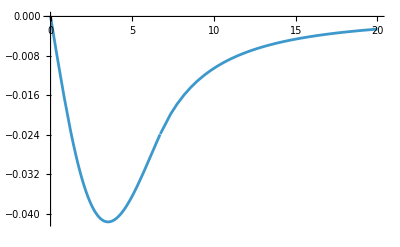

```mathematica
Plot[DERAFull[rbar], {rbar, 0, 20}]
```

### Defining the speed of sound a(r):

```mathematica
drhodr[r_]:= Derivative[1][rhoInside][r]
```

```mathematica
cutoffIso = .99999999rbarStar
```

6.71082

```mathematica
aFirst[rbar_] := Sqrt[dPdr[rofrbarInside[rbar],Pressure[rofrbarInside[rbar]]]/(drhodr[rofrbarInside[rbar]])]
```

```mathematica
aFirst[cutoffIso]
```

0.0000387098

```mathematica
(*Needed to implement these measures to speed things up using Module to avoid recomputation and also the N@ to return numbers instead of symbols for NDSolve, pressure was causing an issue*)
(*Module avoids repeating the calculation three times as there were three arguments I would have had to have inputted it in*)
```

```mathematica
asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]},Piecewise[{
{Sqrt[dPdr[r,Pressure[r]]/drhodr[r]],rbar<cutoffIso},
{aFirst[cutoffIso], rbar >= cutoffIso}
}
]
]
```

```mathematica
(*asosPiecewise[rbar_?NumericQ]:=Module[{r=rofrbarInside[rbar]}, N@Sqrt[dPdr[r,Pressure[r]]/drhodr[r]]]*)
```

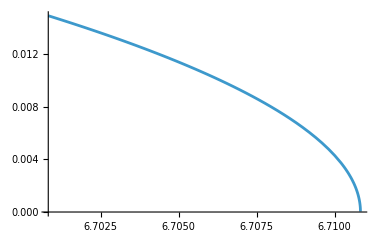

```mathematica
Plot[asosPiecewise[rbar], {rbar, cutoffIso-.01, rbarStar}]
asosPiecewise[rbarStar];
```

## Setting up 2D ODEs for new density profile:

```mathematica
Isorho[rbar_] := Module[{r = rofrbarInside[rbar]}, rho0(1 - alphaaa (r/RStar)^2 + (alphaaa-1)(r/RStar)^4)]
```

```mathematica
IsotropicCoordsPressure[rbar_] := Pressure[rofrbarInside[rbar]]
```

InterpolatingFunction::dmval: Input value {0.000186683} lies outside the range of data in the interpolating function. Extrapolation will be used.

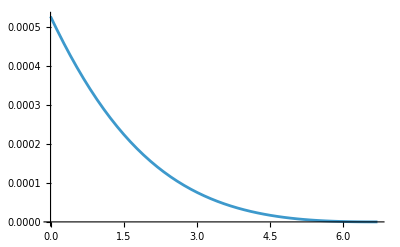

```mathematica
Plot[IsotropicCoordsPressure[rbar], {rbar, 0, rbarStar}]
```

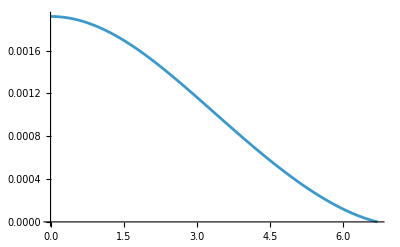

```mathematica
Plot[Isorho[rbar], {rbar, 0, rbarStar}]
```

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=.98;
x2=1.02;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.98},
{anaylticline[Μach], 0.98 < Μach  < 1.02},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.02}
}];
```

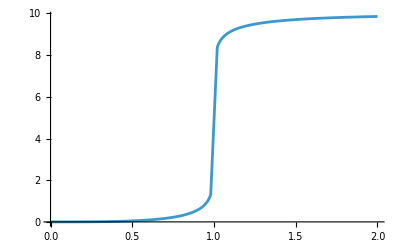

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, Exclusions->None, PlotRange->All]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
umagOutside[rbar_, ur_, uphi_]:=(√(ur^2+(uphi/rbar)^2))/A[rbar]
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] :=umagInside[rbar, ur, uphi]/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative Forces

Accretion

```mathematica
mdot[m_, rbar_, ur_, uphi_] := (4Pi Isorho[rbar] m^2)/((asosPiecewise[rbar]^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/((asosPiecewise[rbar]^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)))uphi
```

Drag

```mathematica
dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(Isorho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);

dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](Isorho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
Mp[r_] := Derivative[1][MassFuncInside][r]
Mpp[r_] := Derivative[2][MassFuncInside][r]
Mppp[r_] := Derivative[3][MassFuncInside][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFuncInside[r]^2+r MassFuncInside[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFuncInside[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFuncInside[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
(*eccentricity = 9/11;*) (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];

(*AngularMomentumUphi0 = infprec[AngularMomentumUphi00, 2];*)
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];

rbar0 //N
rbarStar // N

rperiapsis[eccentricity, ptilde];
```

15.6507

6.71082

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
η = 8 10^3;
```

```mathematica
drBardtInside[rbarStar,0, AngularMomentumUphi0]
durdt2DInside[m, rbarStar,0, AngularMomentumUphi0]
duphidtInside[m, rbarStar,0, AngularMomentumUphi0]
dphidtInside[rbarStar,0, AngularMomentumUphi0]
```

0.

0.00257606

-0.0000498675

0.0491949

```mathematica
t0=0;
tEnd=50000;

NearSubsonicTime = {};

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision(*Machine precision and 20k max steps also works*)
][[1]];
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {7.44297019349186118421861833788816276074228587`15.954589770191005*^139567066496} and/or the interpolation grid is insufficient to compute the value.

NDSolve::nrnum1: The function value -0.98+(5.8499521309340186695290836772`15.954589770191005*^558268265990)/(√(1+(5.1279801231141065915853110361`15.352529778863042*^1116536531972)/(InterpolatingFunction[{«1»},{«13»},{«1»},{«10001»},{«1»}][«79»])^2) «1»[7.44297019349186118421861833788816276074228587`15.954589770191005*^139567066496]) is not a real number when the arguments are {228.343,7.44297019349186118421861833788816276074228587`15.954589770191005*^139567066496,3.042474078353002508205860637707808656`15.954589770191005*^418701199489,1.278185161250424469841135963786894545526139185`15.954589770191005*^139567066497,-1.99398219749742141075869526723673120562`15.954589770191005*^418701199491,1.×10^-6,1,-1,1,1,-1}.

NDSolve::nlnum: The function value $Failed is not a list of numbers with dimensions {5} at {t,rbar[t],ur[t],phi[t],uphi[t],mass[t],NDSolve`s$13349[t],NDSolve`s$13351[t],NDSolve`s$13343[t],NDSolve`s$13350[t],NDSolve`s$13344[t]} = {228.343,{7.442970193491861`15.954589770191005*^139567066496,3.042474078353003`15.954589770191005*^418701199489,1.278185161250424`15.954589770191005*^139567066497,-1.993982197497421`15.954589770191005*^418701199491,1.×10^-6},{1,-1,1,1,-1}}.

225.834

164.465

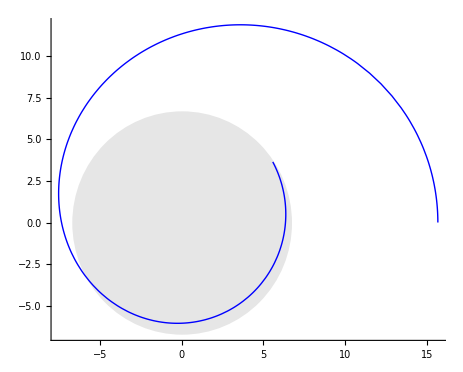

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;

tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]

x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
NearSubsonicTime[[1]]
rbarNumIn[1413]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

InterpolatingFunction::dmval: Input value {1413} lies outside the range of data in the interpolating function. Extrapolation will be used.

-5236.26

```mathematica
Plot[Mach[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t,Part[NearSubsonicTime[[1]], 1], .93tFinish} ,PlotRange->All]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {} in {t,{},210.026} is not a machine-sized real number.

Plot[Mach[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],{t,NearSubsonicTime⟦1⟧⟦1⟧,0.93 tFinish},PlotRange→All]

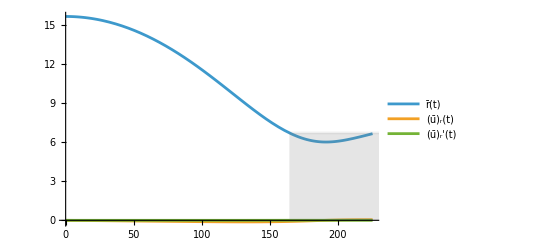

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

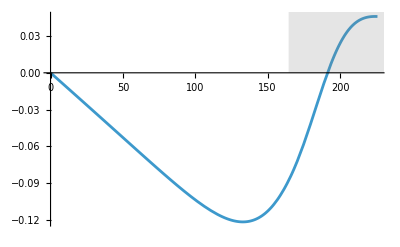

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

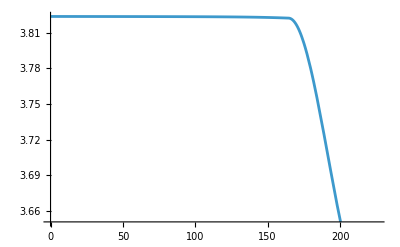

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

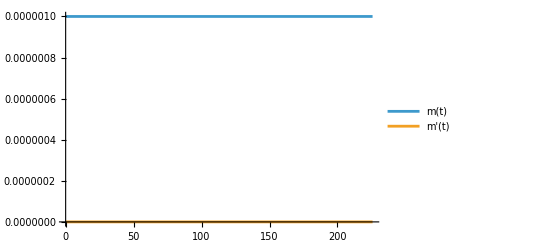

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

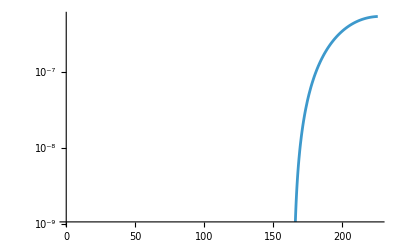

```mathematica
LogPlot[Abs[1 - massNumIn[t]/massNumIn[0]], {t, 0, tFinish}]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

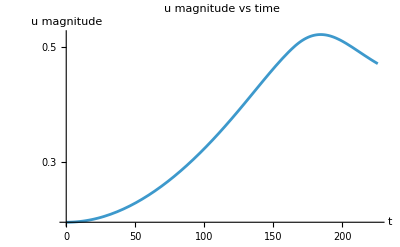

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

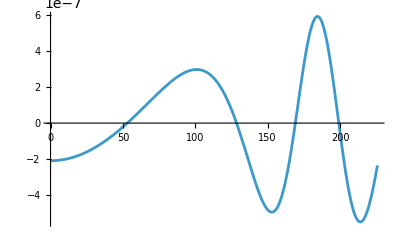

```mathematica
Plot[hplusFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

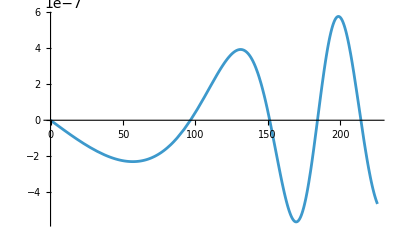

```mathematica
Plot[hxFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

## Energy loss during orbits CHECK angles and other assumptions made by authors for these formulae especially the angular momentum stuff.

### Instantaneous energy loss (coordinate system dependent)

```mathematica
dEdtInside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarInside[rbar],rd,phid},rd=drBardtInside[rbar,ur,uphi];
phid=dphidtInside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(MassFuncInside[r]^2*(8 rd^2+6 (r phid)^2)+r MassFuncInside[r]*(6 rd^4-6 (3(r phid)^4+(r phid)^2 Mp[r])+rd^2 (63 (r phid)^2+Mp[r]-3 r Mpp[r]))+r^2*(6 (r phid)^4 Mp[r]-rd^2 ((Mp[r])^2+3 (r phid)^2 (13 Mp[r]-3 r Mpp[r]))-rd^4 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))]
```

```mathematica
dEdtOutside[m_,rbar_,ur_,uphi_]:=Module[{r=rofrbarOutside[rbar],rd,phid},rd=drBardt[rbar,ur,uphi];
phid=dphidtOutside[rbar,ur,uphi];
(8 m^2)/(15 r^4)*(M^2*(8 rd^2+6 (r phid)^2)+r M*(6 rd^4-6 (3(r phid)^4)+rd^2 (63 (r phid)^2)))]
```

```mathematica
dEdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dEdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dEdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

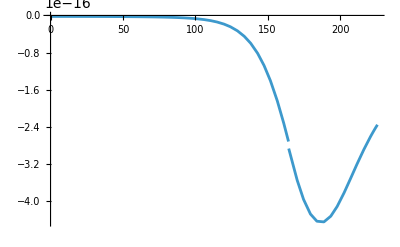

```mathematica
Plot[dEdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

## Angular momentum loss during orbits

### Instantaneous angular momentum loss (coordinate system dependent)

```mathematica
dLdtOutside[m_, rbar_, ur_, uphi_]:= Module[{r=rofrbarOutside[rbar]},
r^2 FRRphi[m, rbar, ur, uphi]]
dLdtInside[m_, rbar_, ur_, uphi_]:= Module[{r=rofrbarInside[rbar]},
r^2 FRRphiIns[m, rbar, ur, uphi]]
```

```mathematica
dLdtFull[m_, rbar_, ur_, uphi_] := Piecewise[
{
{dLdtOutside[m, rbar, ur, uphi], rbar >= rbarStar},
{dLdtInside[m, rbar, ur, uphi], rbar <rbarStar}
}
]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

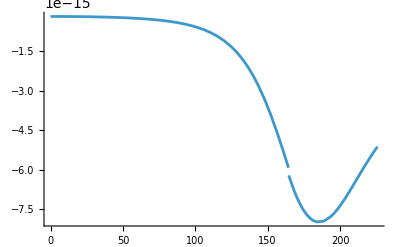

```mathematica
Plot[dLdtFull[massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t, 0, tFinish}, PlotRange->All]
```

## Capturing the PBH from infinity

Assuming PBH comes from infinity and just hits in and enters the star

#### Approaching the problem differently, using Keplerian orbits on the outside of the star and then GR on the inside to reduce the stiffness of the problem causing the error in the solver.

Setting v_inf to something physical is essential, most dark matter comes from the galactic halo, where things move at roughly 200km/s so with setting c = 1, vinf should be 6.67 x 10^-4 which implies the Energy at infinity should be approximately equal to 1 and very little energy loss is needed to bound the orbit.

### Defining Initial Data Functions

```mathematica
vinf = 6.67 10^-4;
```

```mathematica
(*rbar0 = 15.67;*)
```

```mathematica
InitialEnergyAtInfinity[vinf_] := 1/(√(1 - vinf^2)); (*eq47 2404 paper*)
```

```mathematica
(*general formula for the magnitude of the velocity, for a general spherically symmetric Isotropic metric*)
umagVel[ur_, uphi_, rbar_] := √(ur^2 + (uphi/rbar)^2)
umagE[Energy_, rbar_] := A[rbar] √((Energy/α[rbar])^2 - 1); (*eq 48 in paper*)
```

```mathematica
(*Defining the Impact angle, which is the angle between the radial vector and the PBH's velocity vector*) (*It is the angle the PBH enters the star*)

urInit[psi_, Einit_] := -umagE[Einit , rbarStar]Cos[psi];
uphiInit[psi_, rbarStar_, Einit_] := rbarStar umagE[Einit ]Sin[psi]; (*Is defining angular momentum, L is equal to this*)
```

### Setting the Initial conditions

```mathematica
(*we start at rbarStar*)
phi0 = 0;
Einf = InitialEnergyAtInfinity[vinf]//N
 u = umagE[Einf, rbarStar];
ImpactAngle = .85Pi/2; (*In radians, measured from center of star to the position of particle, in unit circle fashion, (*1.5 Pi/4 η = 10^3 is nice*)pi/2 corresponds to grazing the star as it enters and 0 corresponds to a radial drop*)
ur0 = -u*Cos[ImpactAngle];
AngularMomentumUphi0 = (rbarStar)(u) Sin[ImpactAngle];
```

1.

### Sanity Check to see if the two energy formulas match up

```mathematica
Einf = InitialEnergyAtInfinity[vinf] //N
α[rbarStar]^2  Ut[rbarStar, ur0, AngularMomentumUphi0] //N (*This Ut was upper indexed*)
```

1.

1.

### Performing the integration

```mathematica
(*,
Method->{"DiscontinuityProcessing"->False}*)
```

```mathematica
t0=0;
tEnd=100000;
η = 1 10^4;

NearSubsonicTime2 = {};

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== .9999rbarStar,
ur[t0]==ur0,
phi[t0]==phi0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"],
WhenEvent[rbar[t] < 4.7 && Mach[rbar[t], ur[t], uphi[t]] <= 2, AppendTo[NearSubsonicTime2, {t, rbar[t]}]]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->MachinePrecision,
Method->{"DiscontinuityProcessing"->False}
(*Machine precision and 20k max steps also works*)
][[1]];
```

InterpolatingFunction::dmval: Input value {7.68144} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

NDSolve::nbnum1: The function value ComplexInfinity≤2 is not True or False when the arguments are {29.9695,6.71394,0.147482,1.79158,4.30525,1.×10^-6}.

NDSolve::ecboo: The value of event condition function at t = 29.9695 was not True or False. The event will be considered inactive.

Power::infy: Infinite expression 1/0. encountered.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

NDSolve::nbnum1: The function value ComplexInfinity≤2 is not True or False when the arguments are {30.0273,6.71873,0.147894,1.79467,4.30524,1.×10^-6}.

NDSolve::ecboo: The value of event condition function at t = 30.0273 was not True or False. The event will be considered inactive.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

NDSolve::nbnum1: The function value ComplexInfinity≤2 is not True or False when the arguments are {30.1042,6.72514,0.148441,1.79879,4.30524,1.×10^-6}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at t = 30.1042 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

778.344

FindRoot::reged: The point {10.} is at the edge of the search region {10.,778.344} in coordinate 1 and the computed search direction points outside the region.

10.

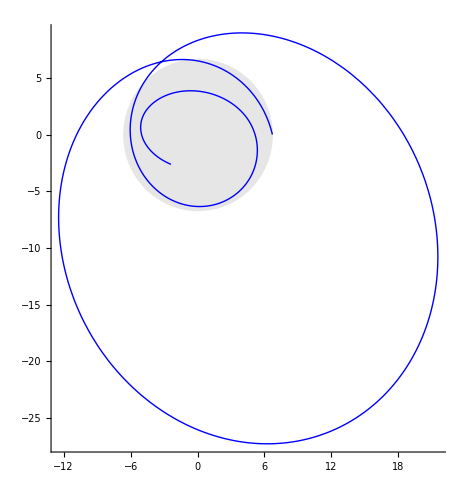

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;

tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]

x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```

```mathematica
NearSubsonicTime[[1]]
rbarNumIn[1475]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

InterpolatingFunction::dmval: Input value {1475} lies outside the range of data in the interpolating function. Extrapolation will be used.

47582.1

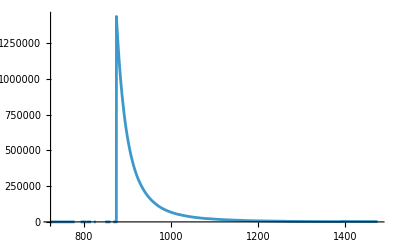

```mathematica
Plot[Mach[rbarNumIn[t], urNumIn[t], uphiNumIn[t]], {t,1475, .93tFinish} ,PlotRange->All]
```

```mathematica
Animate[Show[centralBody, ParametricPlot[{x[s],y[s]},{s,0,t}],PlotRange->All,Axes->True],{t,0,tFinish}]
```

## Stuff

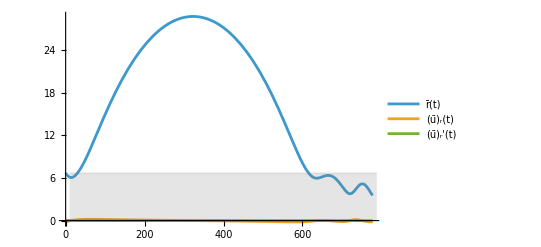

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

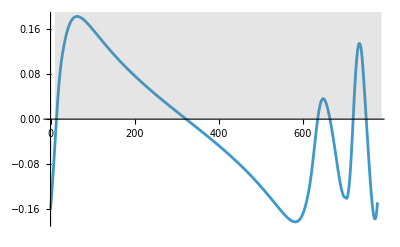

```mathematica
outFigRadial=Show[Plot[{urNumIn[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

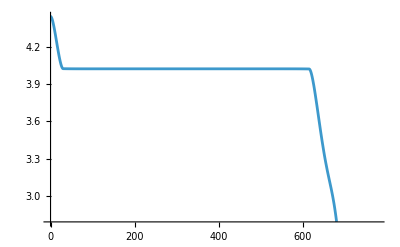

```mathematica
outFigAngular=Plot[{uphiNumIn[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

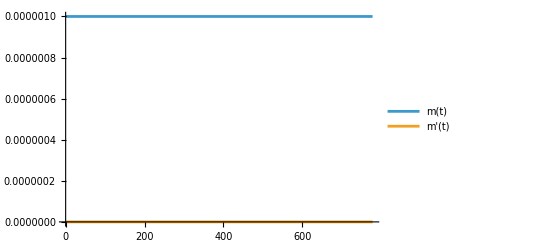

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]]]
```

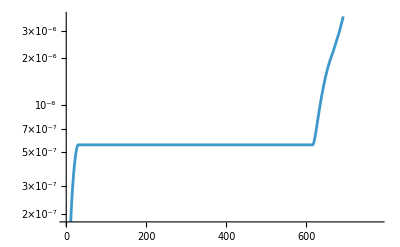

```mathematica
LogPlot[Abs[1 - massNumIn[t]/massNumIn[0]], {t, 0, tFinish}]
```

```mathematica
umag[rbar_, ur_, uphi_] := Piecewise[
{
{umagOutside[rbar, ur, uphi], rbar >= rbarStar},
{umagInside[rbar, ur, uphi], rbar < rbarStar}
}
]
```

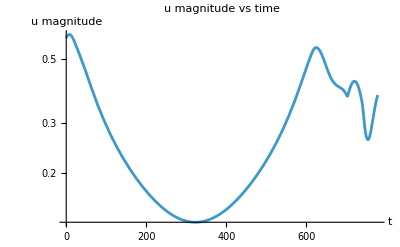

```mathematica
LogPlot[Evaluate[umag[rbarNumIn[t],urNumIn[t],uphiNumIn[t]]/. solIn],{t,0,tFinish},PlotRange->All,AxesLabel->{"t","u magnitude"},PlotLabel->"u magnitude vs time"]
```

```mathematica
(*Show me the value of u at tfinish*)
umag[rbarNumIn[tFinish],urNumIn[tFinish],uphiNumIn[tFinish]]/. solIn
```

0.37412

## Gravitational-wave strains

### h_+

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

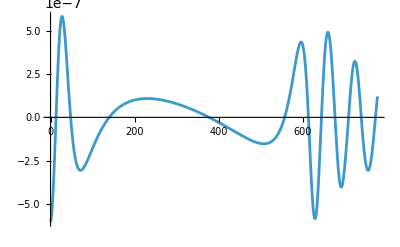

```mathematica
Plot[hplusFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```

### h_x

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((MassFuncInside[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

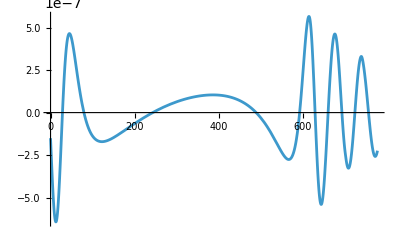

```mathematica
Plot[hxFull[1, massNumIn[t], rbarNumIn[t], urNumIn[t], uphiNumIn[t], phiNumIn[t]], {t, 0, tFinish}, PlotRange->Full, Exclusions->None] (*10^8 it gets jagged*)
```